# The Highway to Hell

## Ringstraße mit Hindernissen

Für eine bessere Lesbarkeit unseres Projekts wird ein Download des benötigten Fonts über den Link https://www.dafontfree.co/downloads/ac-dc/ empfohlen. Hierfür muss die ZIP-Datei ausgeführt und die Dateien “squealer embossed.ttf” und “squealer.ttf” installiert werden.

Die Hälfte der Deutschen verbringen jedes Jahr im Durchschnitt 40 Stunden im Stau. 
Oft bilden sich diese Staus aus dem Nichts. Das Nagel-Schreckenberg-Modell simuliert und analysiert den Verkehr unfallfrei und liefert u.A. eine Erklärung für dieses Phänomen. 

Das NaSch-Modell teilt die Straße in einzelne Abschnitte, die entweder von einem Auto besetzt oder leer sind. Diese Zellen haben eine Länge von 7,5m. Auch die Zeitschritte in Sekunden, oft "Runden" genannt, und Geschwindigkeiten sind diskret, mit Geschwindigkeiten von üblicherweise 0 bis 5. Hierbei entspricht v=0 einem stehenden Auto, v=1 einem Auto, das eine Zelle pro Zeitschritt, also 7,5m/s bzw. 27km/h, fährt. Somit ist die Maximalgeschwindigkeit v=5 umgerechnet 135km/h.

## NaSch-Modell

Das Hauptmodul berechnet die Positionen, Geschwindigkeiten und Abstände der Autos pro diskretem Zeitschritt, die als Runden bezeichnet werden. 
Die Autos werden randomisiert auf der Straße erzeugt (t=0) mit zufällig zugeteilten Geschwindigkeiten. Die Berechnungen finden in einer For-Schleife statt, die die Runden von i=1 bis i=tMax-1 iteriert.
Die erste Regel R1 ist die Beschleunigung von jedem Auto um 1. Falls der Abstand von dem nächsten Auto kleiner als die neue Geschwindigkeit ist, wird in Regel R2 abgebremst. In Regel R3 wird der Verkehr randomisiert - ein Auto kann mit einer Trödelwahrscheinlichkeit p zusätzlich um 1 abbremsen, falls es nicht schon steht. Die Regel R4 aktualisiert die Positionen der Autos.
Die betrachtete Straße ist eine Ringstraße. 
Das Modul wird für alle Plots und Betrachtungen verwendet, die das Nagel-Schreckenberg-Modell auf einer Spur und ohne VDR verwenden.

```mathematica
(*Modul Nagel-Schreckenberg Modell*)
NaSch[nCar_,nCells_,tMax_,vMax_,p_]:=Module[
(*Eingabe Anzahl der Autos nCar, Anzahl der Zellen nCells, Simulationsdauer tMax, 
Maximalgeschwindigkeit vMax und Trödelwahrscheinlichkeit p mit Funktionsaufruf*)

(*lokale Variablen*)
{xAutos,vAutos,dAutos,minAuto,maxAuto,xnasch,vnasch,dnasch},

(*Listen für x, v und d für Berechnungen außerhalb des Moduls*)
xnasch={};
vnasch={};
dnasch={};

(*Autos haben Position x und Geschwindigkeit v zum vorderen Auto*)
xAutos=Sort[RandomSample[Range[nCells],nCar]];
AppendTo[xnasch,xAutos];
(*erzeugt zufällige (Random) Liste xAutos ohne Wiederholungen (Sample) in aufsteigender Reihenfolge (Sort)*)
vAutos=RandomInteger[{1,vMax},nCar];
AppendTo[vnasch,vAutos];
(*ordnet jedem Auto eine zufällige Geschwindigkeit von 0 bis vMax zu*)
(*Einzelne Autos sind gekennzeichnet durch Element-Position in der Liste mit Position xAutos[[n]] und Geschwindigkeit vAutos[[n]]*)

(*Verkehrsregeln aus NaSch-Modell implementieren*)
For[i=1,i<tMax,i++, (*Schleife der Runden bis tMax, Anfangsposition außerhalb Schleife ist t=1, deshalb bis t=tMax-1, sodass Anzahl Runden = tMax*)

(*Oft verwendete Variablen*)
minAuto=Min[xAutos];
maxAuto=Max[xAutos];

If[Length[xAutos]>1,
((*Freie Zellen d vor dem Auto bis zum vorderen*)
dAutos=Table[If[xAutos[[n]]<maxAuto,xAutos[[n+1]]-xAutos[[n]]-1,nCells-xAutos[[n]]+minAuto-1],{n,nCar-1}]; (*In Schleife, damit es geupdatet wird*)
(*berechnet freie Zellen zum vorderen Auto normal außer für Autos außer dem mit höchster Positition - da Ringstraße sind die freien Zellen geringer als xAutos[[n+1]]-xAutos[[n]]-1*)
(*Arrays starten mit Element 1; n+1 muss für das letzte gleich nCar sein*)
AppendTo[dAutos,If[xAutos[[nCar]]<maxAuto,xAutos[[1]]-xAutos[[nCar]]-1,nCells-xAutos[[nCar]]+minAuto-1]];
(*Abstand des Autos an letzter Stelle in Liste zum ersten wird angehängt*)),
dAutos={nCells-1};
];

(*R1: Beschleunigen, falls vMax noch nicht erreicht*)
vAutos=Table[Min[vAutos[[n]]+1,vMax],{n,nCar}];

(*R2: Abbremsen, falls v größer als Abstand d*)
vAutos=Table[Min[dAutos[[n]],vAutos[[n]]],{n,nCar}]; 

(*R3: Trödeln mit Wahrscheinlichkeit p*)
vAutos=Table[If[RandomReal[{0,1}]<=p,vAutos[[n]]=Max[vAutos[[n]]-1,0],vAutos[[n]]],{n,nCar}]; (*Trödeln solange noch nicht v=0*)
(*Falls zufällige Zahl nicht im gegebenen Intervall, bleibt v gleich*)

(*R4: Fahren um vAutos Zellen*)
xAutos=Table[If[xAutos[[n]]+vAutos[[n]]<=nCells,xAutos[[n]]=xAutos[[n]]+vAutos[[n]],xAutos[[n]]=xAutos[[n]]+vAutos[[n]]-nCells],{n,nCar}];
(*Falls Autos außerhalb Zellen bewegt, wird Bewegung in erster Zelle fortgesetzt, da Ringstraße*)
(*Aktualisieren der Positionen nicht anhand Verschieben der Autos innerhalb der Liste, sondern durch Verändern der Einträge in xAutos*)

(*Abspeichern in Variablen*)
AppendTo[xnasch,xAutos];
AppendTo[vnasch,vAutos];
(*Letzter Durchlauf der Schleife speichert vorletzten Abstand ab, deshalb außerhalb Schleife letztes Element abspeichern*)
AppendTo[dnasch,dAutos];
];
(*Erneute Berechnung für Endposition*)
minAuto=Min[xAutos];
maxAuto=Max[xAutos];

(*Berechnen Abstände im letzten Zeitschritt*)
dAutos=Table[If[xAutos[[n]]<maxAuto,xAutos[[n+1]]-xAutos[[n]]-1,nCells-xAutos[[n]]+minAuto-1],{n,nCar-1}];
AppendTo[dAutos,If[xAutos[[nCar]]<maxAuto,xAutos[[1]]-xAutos[[nCar]]-1,nCells-xAutos[[nCar]]+minAuto-1]];

(*Abspeichern in dnasch*)
AppendTo[dnasch,dAutos];

Return[{xnasch,vnasch,dnasch}]
]
```

```mathematica
nasch100=NaSch[100,300,100,5,0.15];
```

Die Daten aus dem ersten Aufruf werden für alle Plots, die die gleichen Eingabeparameter (100 Autos, 300 Zellen, 100 Runden, vMax=5 und p=0.15) fordern, verwendet.

## Grafische Darstellung der Straße

Das Modul densityplot stellt die Straße über die Zeit grafisch dar mit besetzte Zellen in hell und leere Zellen in dunkelrot.

```mathematica
(*Für NaSch-Modell ohne VDR q=0*)
densityplot[Modell_,nCar_,p_,q_]:=Module[
{nCells,tMax,vMax,strasse,newstrasse,listdensityplot,nasch},

(*Variablen aus vorherigem NaSch-Aufruf*)
nCells=300;
tMax=100;
vMax=5;

(*Daten aus Berechnungen nasch oder vdr*)
nasch=Which[Modell=="NaSch",Which[!p==0.15,NaSch[nCar,nCells,tMax,vMax,p][[1]],p==0.15 && !nCar==100,NaSch[nCar,nCells,tMax,vMax,p][[1]],p==0.15 && nCar==100,nasch100[[1]]],
Modell=="vdrNaSch",vdrNaSch[nCar,nCells,tMax,vMax,p,q][[1]]];

(*Sortierte Liste der Straße mit leeren Zellen als 0 und besetzt als 1*)
strasse=Table[Table[If[Select[nasch[[m]],#==n &]=={},0,1],{n,1,nCells}],{m,tMax}]; 

(*Anpassen strasse sodass t in positive x-Richtung läuft statt in positiver y-Richtung*)
newstrasse=Table[Table[strasse[[n,m]],{n,tMax}],{m,nCells}];

(*ListDensityPlot*)
listdensityplot=ListDensityPlot[newstrasse,FrameLabel->{"Zeit t","Zellen der Straße"},ImageSize->Medium,PlotLegends->Automatic,
PlotLabel->ToString[Modell]<>": Grafische Darstellung der Straße mit "<>ToString[nCar]<>" Autos und p="<>ToString[p],ColorFunction->"SolarColors",
LabelStyle->White];
Return[listdensityplot]
]
```

```mathematica
listdensityplot=densityplot["NaSch",100,0.15,0];
Show[listdensityplot]
```

-Graphics-

Das Modul densityplot stellt die Straße über die Zeit dar. Auf der y-Achse sind die Zellen der Straße mit besetzten Zellen als gelbe Punkte und leere als dunkelrote Punkte. Die Entwicklung über die Zeit ist in positiver x-Richtung aufgetragen. Es lässt sich beobachten, dass eine Ansammlung von Autos bei t=0 in der Grafik in positiver x-Richtung nach unten wandert, indem Autos aus den vorderen Zellen der Ansammlung losfahren und die hinteren sich stauen bzw neue Autos auf den Stau auffahren.
Zu sehen sind mehrere Ansammlungen an Autos zu Beginn der Simulation. Von hinten auffahrende Autos werden ausgebremst und Autos am vorderen Ende der Ansammlung beschleunigen, weshalb sich die Ansammlungen im Laufe der Zeit in negativer y-Richtung verlagern - es bilden sich Rückstaus.

## Dichteplot

Das Modul dichteplot, so wie densityplot, stellt die Straße über die Zeit dar. Hier werden jedoch jeweils eine Anzahl von avCells Zellen betrachtet, die Anzahl an Autos darin aufsummiert, und dies als Wert ausgegeben.

```mathematica
(*Dichteplot über Zeit*)
dichteplot[Modell_,nCar_,p_,q_,avCells_]:=Module[
(*lokale Variablen*)
{nCells,tMax,vMax,anzahl,laengen,iter,t,cell,nasch},

(*Variablen aus vorherigem NaSch-Aufruf*)
nCells=300;
tMax=100;
vMax=5;

(*Daten Eingabe*)
nasch=Which[Modell=="NaSch",Which[!p==0.15,NaSch[nCar,nCells,tMax,vMax,p][[1]],p==0.15 && !nCar==100,NaSch[nCar,nCells,tMax,vMax,p][[1]],p==0.15 && nCar==100,nasch100[[1]]],
Modell=="vdrNaSch",vdrNaSch[nCar,nCells,tMax,vMax,p,q][[1]]];

(*Liste Anzahl Autos innerhalb Intervall avCells und das pro Zeitschritt*)
laengen={};

(*Anzahl der Intervalle avCells in nCells=iter, Anzahl Autos innerhalb Intervall=anzahl*)
iter=0;t=1;anzahl=0;
(*For-Schleife für einzelne Intervalle mit Länge avCells*)
For[cell=1+iter,cell<=avCells+iter,cell++,
(*Falls Auto auf Zelle, Anzahl erhöhen*)
If[Select[nasch[[t]],#==cell &]!={},anzahl=anzahl+1,anzahl=anzahl];
(*Falls letzte Zelle des Intervalls betrachtet, Anzahl abgespeichert, wieder auf 0*)
If[Divisible[cell,avCells],
AppendTo[laengen,anzahl];
anzahl=0;
(*Falls letzte Subliste in xnasch betrachtet, nächsten Intervall betrachten ab erster Subliste mit t=1*)
If[t==tMax,
(iter=iter+avCells;
If[iter>nCells-avCells,Break[]];
t=1;),
(*Sonst: nächste Subliste betrachten mit gleichem Intervall*)
t=t+1;];
(*Betrachten erste Zelle im Intervall für nächsten Durchgang*)
cell=1+iter;
];
];
(*Ergebnis ist Liste mit Anzahlen der Autos von Zelle 0 bis avCells für t=1,2,3,..., dann von Zelle avCells+1 bis 2 avCells usw.*)
(*Aufteilen laengen in Sublisten für die Intervalle*)
laengen=Partition[laengen,tMax];

listdichteplot=ListDensityPlot[laengen,FrameLabel->{"Zeit t","Intervalle"},ImageSize->Medium,
PlotLabel->ToString[Modell]<>": Dichteplot mit Intervalllänge "<>ToString[avCells]<>", p="<>ToString[p]<>", und q="<>ToString[q],PlotLegends->Automatic,LabelStyle->White,ColorFunction->"SolarColors"];
Return[listdichteplot]
]
```

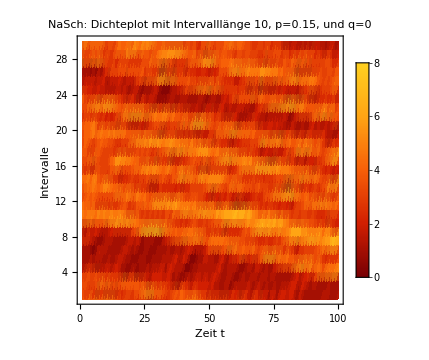

```mathematica
listdichteplot=dichteplot["NaSch",100,0.15,0,10];
Show[listdichteplot]
```

Der Plot zeigt wie erwartet die Ansammlungen vieler Autos aus dem Densityplot oben auch hier als helle, gelbe Punkte (7-8 Autos pro Bereich), sowie Bereiche mit einer geringen Autodichte als dunkelrote Bereiche (0-1 Autos pro Bereich). Die gelben Bereiche sind wie die starken Anstauungen im Dichteplot schräg angeordnet, je weiter die Zeit fortschreitet, desto weiter bilden sich Rückstaus auf Zellen mit niedrigerem Index. Der Großteil der Punkte ist jedoch eingefärbt in orange, also mit 3-4 Autos im betrachteten Bereich.

Das Modul dichteplot2D erstellt nach dem gleichen Schema wie oben einen Dichteplot pro Spur für die Simulation einer zweispurigen Straße anhand des Moduls twolanesNaSch. Es wird weiter unten für die Auswertung dieses Moduls verwendet.

```mathematica
(*Dichteplot über Zeit der zwei Spuren getrennt*)
dichteplot2D[nCar_,p_,avCells_]:=Module[
(*lokale Variablen*)
{nCells,tMax,vMax,anzahl,laengen,iter,t,k,cell,nasch},

(*Variablen aus vorherigem NaSch-Aufruf*)
nCells=150;
tMax=100;
vMax=5;

(*Liste Plots*)
listdichteplot={};

(*Daten Eingabe*)
nasch=twolanesNaSch[nCar,nCells,tMax,vMax,p];
nasch=Take[nasch,{1,2}];

(*Liste Anzahl Autos innerhalb Intervall avCells und das pro Zeitschritt*)
laengen={};

(*Index f+r separates Betrachten der Spuren*)
k=1;
Do[
(*Anzahl der Intervalle avCells in nCells=iter, Anzahl Autos innerhalb Intervall=anzahl*)
iter=0;t=1;anzahl=0;
(*For-Schleife für einzelne Intervalle mit Länge avCells*)
For[cell=1+iter,cell<=avCells+iter,cell++,
(*Falls Auto auf Zelle, Anzahl erhöhen*)
If[Select[nasch[[k,t]],#==cell &]!={},anzahl=anzahl+1,anzahl=anzahl];
(*Falls letzte Zelle des Intervalls betrachtet, Anzahl abgespeichert, wieder auf 0*)
If[Divisible[cell,avCells],
AppendTo[laengen,anzahl];
anzahl=0;
(*Falls letzte Subliste in xnasch betrachtet, nächsten Intervall betrachten ab erster Subliste mit t=0*)
If[t==tMax,
(iter=iter+avCells;
If[iter>nCells-avCells,Break[]];
t=1;),
(*Sonst: nächste Subliste betrachten mit gleichem Intervall*)
t=t+1;];
(*Betrachten erste Zelle im Intervall für nächsten Durchgang*)
cell=1+iter;
];
];
k=2;,2];
(*Ergebnis ist Liste mit Anzahlen der Autos von Zelle 0 bis avCells für t=1,2,3,..., dann von Zelle avCells+1 bis 2 avCells usw.*)
(*Aufteilen laengen in abwechselnde Sublisten der Spuren für die Intervalle*)
laengen=Partition[laengen,tMax];

AppendTo[listdichteplot,ListDensityPlot[Take[laengen,nCells/avCells],FrameLabel->{"Zeit t","Intervalle"},ImageSize->Medium,
PlotLabel->"twolanesNaSch Spur 1: Dichteplot mit Intervalllänge "<>ToString[avCells]<>"\n und p="<>ToString[p],PlotLegends->Automatic,LabelStyle->White,ColorFunction->"SolarColors"]];
AppendTo[listdichteplot,ListDensityPlot[Drop[laengen,nCells/avCells],FrameLabel->{"Zeit t","Intervalle"},ImageSize->Medium,
PlotLabel->"twolanesNaSch Spur 2: Dichteplot mit Intervalllänge "<>ToString[avCells]<>"\n und p="<>ToString[p],PlotLegends->Automatic,LabelStyle->White,ColorFunction->"SolarColors"]];
Return[listdichteplot]
]
```

## Histogramme

In diesem Modul werden Histogramme der Geschwindigkeit und des Abstand für die Autoanzahlen in carlist, die Zeitpunkte in tlist und die Trödelwahrscheinlichkeit p und für das VDR-Modell die zusätzliche Trödelwahrscheinlichkeit q erstellt. Falls Histogramme für die oben berechneten Autoanzahlen erstellt werden sollen, wird auf diese Daten in der Liste histonasch zugegriffen.

```mathematica
(*Daten NaSch-Modell für nCar=60,100,200*)
histonasch={NaSch[60,300,100,5,0.15],nasch100,NaSch[200,300,100,5,0.15]};
```

```mathematica
(*Falls Modell NaSch, q=0*)
vdhisto[Modell_,carlist_,tlist_,p_,q_]:=Module[
(*tlist sind Zeitpunkte, für die Histogramme zu bestimmen sind; auch einzelnen Zeitpunkt als Liste eingeben*)

(*lokale Variablen*)
{nCells,nCar,tMax,vMax,anzahlt,anzahlcars,zeit,viAutos,diAutos,i,vhisto,dhisto,histoplot,nasch},

(*Variablen aus vorherigem NaSch-Aufruf*)
nCells=300;
tMax=100;
vMax=5;

(*Listen der Plots*)
histoplot={};
anzahlt=Length[tlist];
anzahlcars=Length[carlist];

(*Für betrachtete Anzahlen Autos*)
For[k=1,k<=anzahlcars,k++,

(*Anzahl Autos*)
nCar=carlist[[k]];

(*Daten aus Berechnungen nasch oder vdr*)
nasch=Which[Modell=="NaSch",Which[p==0.15,Which[!MemberQ[{60,100,200},nCar],NaSch[nCar,nCells,tMax,vMax,p],nCar==60,histonasch[[1]],nCar==100,histonasch[[2]],nCar==200,histonasch[[3]]],
!p==0.15,NaSch[nCar,nCells,tMax,vMax,p]],Modell=="vdrNaSch",vdrNaSch[nCar,nCells,tMax,vMax,p,q]];

For[j=1,j<=anzahlt,j++,
(*Betrachtete Zeit*)
zeit=tlist[[j]];
(*Listen Autos mit Geschwindigkeiten v=0,1,2,3,4,5*)
Clear[viAutos];
viAutos=Table[Select[Table[nasch[[2,zeit,n]],{n,1,nCar}],#==i &],{i,0,5}];

(*Listen Abstände d=0,1,...,nCar*)
Clear[diAutos];
diAutos=Select[Table[Select[Table[nasch[[3,zeit,n]],{n,1,nCar}],#==i &],{i,0,Max[nasch[[3,zeit]]]}],UnsameQ[#, {}] &]; 
(*Löschen der Abstände, die nicht vorkommen*)

AppendTo[histoplot,Histogram[viAutos,{1},AxesLabel->{v,Anzahl Autos mit Indexed[v,"i"]},ColorFunction->"SolarColors",PlotRange->{{Automatic,5.5},Automatic},ImageSize->Medium,
PlotLabel->ToString[Modell]<>": Histogramm von v\n mit "<>ToString[nCar]<>" Autos, t="<>ToString[zeit]<>",\n p="<>ToString[p]<>", q="<>ToString[q],LabelStyle->White]];
AppendTo[histoplot,Histogram[diAutos,{1},AxesLabel->{d,Anzahl Autos mit Indexed[d,"i"]},ColorFunction->"SolarColors",PlotRange->{0,All},ImageSize->Medium,
PlotLabel->ToString[Modell]<>": Histogramm von d\n mit "<>ToString[nCar]<>" Autos, t="<>ToString[zeit]<>",\n p="<>ToString[p]<>", q="<>ToString[q],LabelStyle->White]];
(*Histogramm zählt, wie oft eine Zahl in einer Liste und den Sublisten darin vorkommt*)
];];
Return[histoplot]
]
```

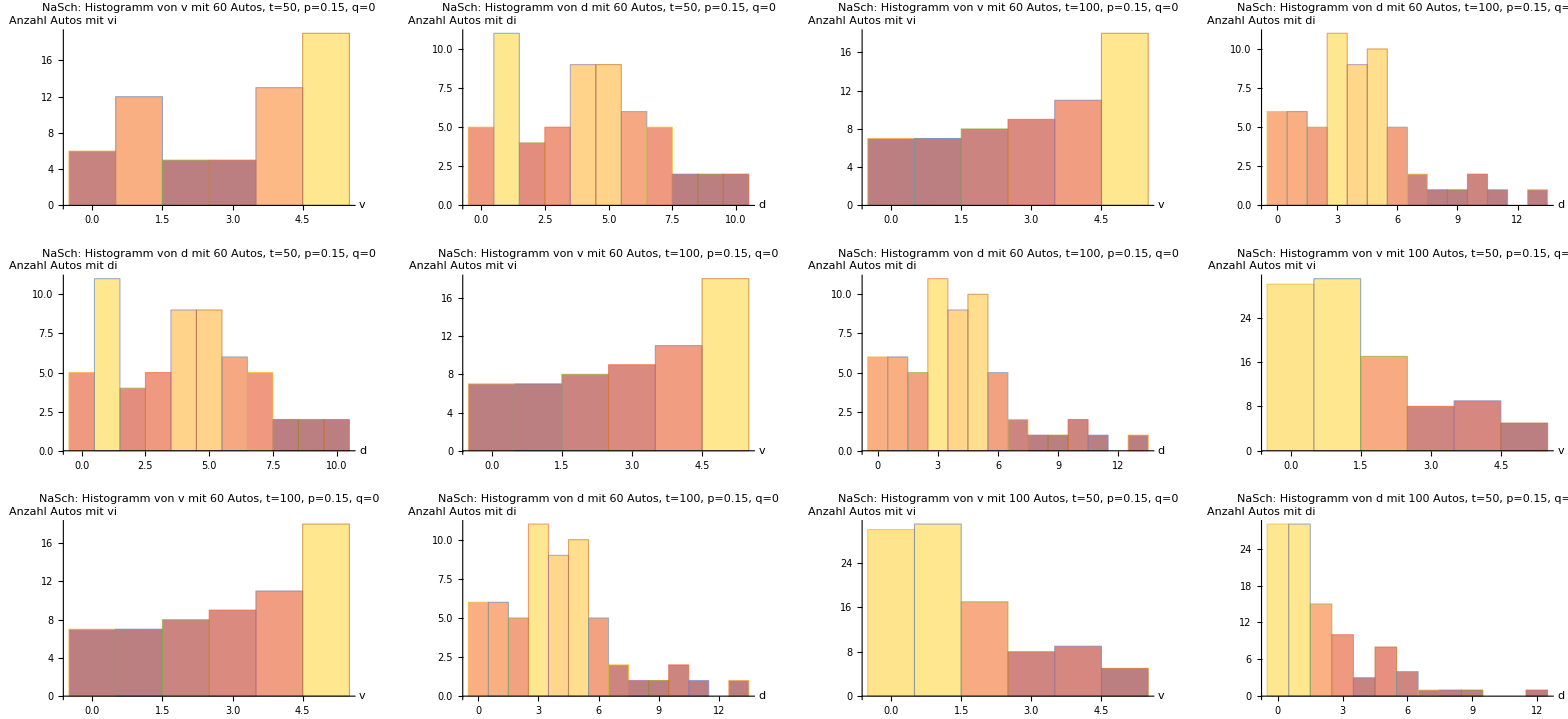

```mathematica
histoplot=vdhisto["NaSch",{60,100,200},{50,100},0.15,0];
GraphicsGrid[Table[{histoplot[[i]],histoplot[[i+1]],histoplot[[i+2]],histoplot[[i+3]]},{i,3}],ImageSize->Full]
```

```mathematica
Clear[histoplot];
```

Aus den Histogrammen der Abstände lässt sich beobachte, dass je größer der Abstand zwischen den Autos ist, desto weniger mit diesem Abstand vorhanden sind aufgrund der festen Anzahl der Zellen. Dieser Effekt wird umso stärker, je höher die Anzahl der Autos ist. Bei 60 Autos haben hingegen ein Drittel der Autos einen Abstand, der größer als die Maximalgeschwindigkeit 5 ist.
Die Histogramme der Geschwindigkeiten bestätigen dies. Mit steigender Autoanzahl steigt der Anteil der Autos, die die Geschwindigkeit 1 oder 0 besitzen, stark an, während bei 60 Autos bei der Hälfte der gesamten Laufzeit (t=50) circa die Hälfte der Autos die Geschwindigkeit 4 oder 5 haben.

In diesem Modul werden Histogramme für die zweispurige Simulation erstellt. Hierbei werden die Spuren getrennt betrachtet. Es wird für das Betrachten des Moduls twolanesNaSch weiter unten verwendet.

```mathematica
(*Histogramme für beide Spuren getrennt*)
vdhisto2D[carlist_,tlist_,p_]:=Module[
(*tlist sind Zeitpunkte, für die Histogramme zu bestimmen sind; auch einzelnen Zeitpunkt als Liste eingeben*)

(*lokale Variablen*)
{nCells,nCar,tMax,vMax,anzahlt,anzahlcars,zeit,viAutos,diAutos,i,l,vhisto,dhisto,histoplot,nasch},

(*Variablen aus vorherigem NaSch-Aufruf*)
nCells=150;
tMax=100;
vMax=5;

(*Listen der Plots*)
histoplot={};
anzahlt=Length[tlist];
anzahlcars=Length[carlist];

(*Für betrachtete Anzahlen Autos*)
For[k=1,k<=anzahlcars,k++,

(*Anzahl Autos*)
nCar=carlist[[k]];

(*Daten aus Berechnungen nasch oder vdr*)
nasch=twolanesNaSch[nCar,nCells,tMax,vMax,p];
(*Nur Geschwindigkeiten und Abstände aus Ausgabe auswählen*)
nasch=Delete[nasch,{{1},{2},{7},{8},{9},{10}}];

(*Schleife für zwei Spuren*)
For[l=0,l<=1,l++,
(*Schleife für verschiedene Zeitpunkte*)
For[j=1,j<=anzahlt,j++,
(*Betrachtete Zeit*)
zeit=tlist[[j]];
(*Histogramm erstellen, falls Spur nicht leer*)
If[nasch[[1+l,zeit]]=={0.5},Print["Spur ",l+1," ist leer für t=",tlist[[j]],"."];,
(*Anzahl Autos auf Spur bei Zeit t*)
nCar=Length[nasch[[1+l,zeit]]];
(*Listen Autos mit Geschwindigkeiten v=0,1,2,3,4,5*)
Clear[viAutos];
viAutos=Table[Select[Table[nasch[[1+l,zeit,n]],{n,1,nCar}],#==i &],{i,0,5}];

(*Listen Abstände d=0,1,...,nCar*)
Clear[diAutos];
diAutos=Select[Table[Select[Table[nasch[[3+l,zeit,n]],{n,1,nCar}],#==i &],{i,0,Max[nasch[[3+l,zeit]]]}],UnsameQ[#, {}] &]; 
(*Löschen der Abstände, die nicht vorkommen*)

AppendTo[histoplot,Histogram[viAutos,{1},AxesLabel->{v,Anzahl Autos mit Indexed[v,"i"]},ColorFunction->"SolarColors",PlotRange->{{Automatic,5.5},Automatic},ImageSize->Medium,
PlotLabel->"twolanesNaSch Spur "<>ToString[l+1]<>": Histogramm von v\n mit "<>ToString[nCar]<>" Autos, t="<>ToString[zeit]<>", p="<>ToString[p],LabelStyle->White]];
AppendTo[histoplot,Histogram[diAutos,{1},AxesLabel->{d,Anzahl Autos mit Indexed[d,"i"]},ColorFunction->"SolarColors",PlotRange->{0,All},ImageSize->Medium,
PlotLabel->"twolanesNaSch Spur "<>ToString[l+1]<>": Histogramm von d\n mit "<>ToString[nCar]<>" Autos, t="<>ToString[zeit]<>", p="<>ToString[p],LabelStyle->White]];
(*Histogramm zählt, wie oft eine Zahl in einer Liste und den Sublisten darin vorkommt*)
];];];];
Return[histoplot]
]
```

## Meanvarfluss

Hier werden: die mittlere Geschwindigkeit der Autos, die Varianz des Abstands zwischen jedem Auto und der Verkehrsfluss für jede Runde berechnet.
Der Verkehrsfluss ist die Anzahl an Autos, die über die letzte Zelle hinaus wieder an den Anfang der Straße fahren. Pro Zeitschritt kann er auf einer Spur also entweder 0 oder 1 sein.
Anschließend werden Geschwindigkeit und Varianz korreliert. Der Fluss pro Zeitschritt wird auch dargestellt.

```mathematica
(*Berechnung mittlere v über t, Varianz des mittleren Abstands und des Verkehrsflusses über t*)
(*Falls Modell NaSch, q=0*)
Meanvarfluss[Modell_,nCar_,p_,q_]:=Module[
(*betrachtete Zelle für den Fluss ist die letzte Zelle der Straße*)

(*lokale Variablen*)
{nCells,tMax,vMax,vMittel,dVar,nasch,savefluss,savexAutos,m,meanvarflussplot,meanvarkorrplot},

(*Variablen aus vorherigem NaSch-Aufruf*)
nCells=300;
tMax=100;
vMax=5;

(*Liste für Fluss pro Zeitschritt*)
savefluss={};
dVar={};
vMittel={};

(*Daten aus Berechnungen nasch oder vdr*)
nasch=Which[Modell=="NaSch",Which[p==0.15,Which[!MemberQ[{60,100,200},nCar],NaSch[nCar,nCells,tMax,vMax,p][[1]],nCar==60,histonasch[[1]],nCar==100,histonasch[[2]],nCar==200,histonasch[[3]]],
!p==0.15,NaSch[nCar,nCells,tMax,vMax,p]],Modell=="vdrNaSch",vdrNaSch[nCar,nCells,tMax,vMax,p,q]];

(*Erstes Auto, das die letzte Zelle passiert, ist das mit höchster Position*)
m=nCar;

For[t=1,t<=tMax,t++,
(*Verkehrsfluss durch letzte Zelle*)
(*Überprüft, ob Auto mit höchster Position über Straßenende hinaus auf den Anfang zurück gefahren ist 
ja: nächst niedrigeres Auto wird betrachtet + fluss 1 hinzufügen, 
nein: Auto wird weiter betrachtet + fluss 0 hinzufügen
Index m geht Autos vom letzten Element bis zum ersten durch, danach wieder Start bei letztem*)
If[t<tMax,
If[m==0,m=nCar,m=m];
If[nasch[[1,t+1,m]]<nasch[[1,t,m]],
AppendTo[savefluss,1];
m=m-1;,
AppendTo[savefluss,0];
];];

(*mittlere Geschwindigkeit*)
AppendTo[vMittel, N[Mean[nasch[[2,t]]],6]];
(*Varianz dAutos*)
AppendTo[dVar, N[Variance[nasch[[3,t]]],6]];
];

meanvarflussplot=ResourceFunction["PlotGrid"][{
{ListPlot[vMittel,ImageSize->Automatic,ColorFunction->"SolarColors",Frame->True,FrameLabel->{None,"mittlere Geschwindigkeit "OverBar[v]},LabelStyle->White]},
{ListPlot[dVar,ImageSize->Automatic,ColorFunction->"SolarColors",Frame->True,FrameLabel->{None,"Varianz des Abstands d"},LabelStyle->White]},
{ListPlot[savefluss,ImageSize->Automatic,ColorFunction->"SolarColors",Frame->True,FrameLabel->{None,"Fluss pro Zeitschritt"},LabelStyle->White]}
},
ImageSize->Large,FrameLabel->{"Zeit t",None},LabelStyle->White
];

(*Korrelation mittlere Geschwindigkeit und Varianz des Abstands*)
meanvarkorrplot=ListPlot[Thread[{dVar,vMittel}],ImageSize->Large,ColorFunction->"SolarColors",Frame->True,FrameLabel->{"Varianz des Abstands d","mittlere Geschwindigkeit " OverBar[v]},
PlotLabel->ToString[Modell]<>": Korrelation Varianz von d und mittlere v",LabelStyle->White];
Return[{meanvarflussplot,meanvarkorrplot}]
]
```

-Graphics-

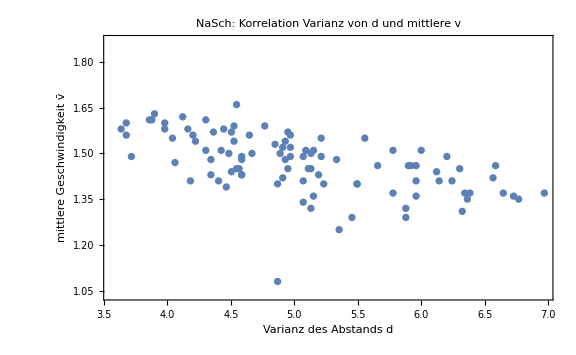

```mathematica
meanvarfluss=Meanvarfluss["NaSch",100,0.15,0];
Show[meanvarfluss[[1]]]
Show[meanvarfluss[[2]]]
```

```mathematica
Clear[meanvarfluss];
```

Am Plot der mittleren Geschwindigkeit lässt sich erkennen, dass sich diese für fast alle Zeitschritte mit wenigen Ausreißern in einem Bereich von Δv=0.4 Zellen/Zeitschritt befindet. Die Varianz des Abstands ist stets in einem Intervall von Δd=5 Zellen. Eine niedrige Varianz ergibt sich entweder, wenn der Verkehr ohne viele Staus fließt oder wenn sich mehrere Staus auf der Straße ausgebildet haben. Eine hohe Varianz dagegen kann von einem Stau auf der Straße, dessen voranfahrende Autos wieder beschleunigen und den Abstand erhöhen, hervorgerufen werden. Die meisten Punkte befinden sich um die Varianz herum die in der Mitte zwischen der niedrigsten und der höchsten Varianz liegt.
Die Grafik des Flusses zeigt, wie dieser nur 1 oder 0 sein kann, weil nur eine Spur simuliert wird. Da ein Auto nur bis zu einer Zelle vor dem nächsten fahren kann (R2: Abbremsen, falls v größer als d), kann eine Zelle in einer Runde nur von einem Auto durchquert werden.
Aus der Korrelation der Geschwindigkeit und der Varianz des Abstands ist zu sehen, wie die mittlere Geschwindigkeit linear abnimmt mit der Zunahme der Varianz des Abstands.

## Fundamentalplot

Unter dem Fundamentalplot versteht man die Korrelation zwischen dem Verkehrsfluss und der Dichte über die gesamte Straße. In diesem Teil wird ein Modul dafür hergestellt und anschließend das dargestellt.
Danach wird es für unterschiedliche Trödelwahrscheinlichkeiten p geschrieben und geplottet.

```mathematica
(*Daten für Fundamentalplots aus histonasch*)
fundnasch60=histonasch[[1,1]];
fundnasch100=histonasch[[2,1]];
fundnasch200=histonasch[[3,1]];
```

```mathematica
(*Fundamentalplot*)
(*Eingabe: Falls Modell NaSch q=0*)
FundamentalD[Modell_,p_,q_]:=Module[
(*Fluss wird für Dichten 0 bis 1 berechnet*)

(*lokale Variablen*)
{nCells,nCar,tMax,vMax,anzahlp,density,addfluss,addfluss1,addfluss2,m,m1,m2,fluss,funddata,fundplot,nasch,nasch1,nasch2,
tnasch,tnasch1,tnasch2,nexttnasch1,nexttnasch2,nexttnasch,mlist1,mlist2,mdiff1,mdiff2,range,nichts,indexfl1,indexfl2,nextindexfl1,nextindexfl2,Zellen,
max1,max2,wechselvon1,wechselzu1,wechselvon2,wechselzu2,index1,nextindex1,index2,nextindex2,vornasch1,vornasch2,vormax1,vormax2,posvormax1,posvormax2},

(*Variablen aus vorherigem NaSch-Aufruf*)
If[Modell!="twolanesNaSch",nCells=300,nCells=150]; (*Für geringere Laufzeit auf zwei Spuren insgesamt 300 Zellen*)
tMax=100;
vMax=5;

(*Erstes Element in Subliste ist Dichte, zweites Fluss*)
funddata={{0,0}};

(*Anzahl Zellen für Modell*)
Zellen=Which[Modell!="twolanesNaSch",nCells,Modell=="twolanesNaSch",2 nCells];

(*Schleife für ansteigende Dichte/Anzahlen an Autos*)
For[nCar=1,nCar<Zellen,nCar++,

(*Berechnen NaSch-Modell, VDR-Modell oder Abrufen berechnete Daten aus histonasch*)
nasch=Which[Modell=="NaSch",Which[p==0.15,Which[!MemberQ[{60,100,200},nCar],NaSch[nCar,nCells,tMax,vMax,p][[1]],nCar==60,fundnasch60,nCar==100,fundnasch100,nCar==200,fundnasch200],
!p==0.15,NaSch[nCar,nCells,tMax,vMax,p][[1]]],Modell=="vdrNaSch",vdrNaSch[nCar,nCells,tMax,vMax,p,q][[1]],Modell=="twolanesNaSch",twolanesNaSch[nCar,nCells,tMax,vMax,p]];

(*Falls twolanesNaSch, extrahieren xAutos und mlisten*)
If[Modell=="twolanesNaSch",nasch1=nasch[[1]];nasch2=nasch[[2]];wechselvon1=nasch[[7]];wechselzu1=nasch[[8]];wechselvon2=nasch[[9]];wechselzu2=nasch[[10]];Clear[nasch];];

(*Index zum Überprüfen der Positionen, startet von der überprüften Zelle nCells; Fluss als Durchfluss von Position nCells zu 1*)
m=nCar;
addfluss=0;
addfluss1=0;
addfluss2=0;
m1=0;
m2=0;

(*Schleife über Zeit für Berechnung des Flusses*)
For[t=1,t<tMax,t++, (*Vergleich mit Zeitschritt danach, also bis tMax-1*)

If[Modell!="twolanesNaSch",
(*Eine Spur*)
((*Abspeichern zu betrachtende Listen*)
tnasch=nasch[[t]];
nexttnasch=nasch[[t+1]];

If[m==0,m=nCar,m=m];
If[nexttnasch[[m]]<tnasch[[m]],
addfluss=addfluss+1;
m=m-1;];),
(*Zwei Spuren*)
If[t>1,
vornasch1=nasch1[[t-1]];
vornasch2=nasch2[[t-1]];
tnasch1=nasch1[[t]];
nexttnasch1=nasch1[[t+1]];
tnasch2=nasch2[[t]];
nexttnasch2=nasch2[[t+1]];
(*Rechte Spur*)
(*Falls eine der beiden Listen leer, 0.5 in zwei Spuren angehängt, falls Spur leer*)
Which[tnasch1=={0.5}||nexttnasch1=={0.5},addfluss1=addfluss1;,
tnasch1!={0.5},
(*vormax1: Position Maximum von t-1, falls zuvor leer 0; posvormax1: Maximum von t-1, falls zuvor leer nCells+1, sodass jeder Wechsel Index erhöht*)
Which[vornasch1!={0.5},(vormax1=Flatten[Position[vornasch1,Max[vornasch1]]][[1]];posvormax1=vornasch1[[vormax1]];),vornasch1=={0.5},(posvormax1=nCells+1;vormax1=0;)];
(*Index Maximum von t-1 mit Wechseln aus Schritt von t-1 bis t*)
index1=vormax1+Length[Select[wechselzu1[[t-1]],#<=posvormax1&]]-Length[Select[wechselvon1[[t-1]],#<=posvormax1&]];
(*Position Maximum von t*)
max1=Flatten[Position[tnasch1,Max[tnasch1]]][[1]];
(*Index Maximum von t mit Wechseln aus Schritt von t bis t+1*)
nextindex1=max1+Length[Select[wechselzu1[[t]],#<=tnasch1[[max1]]&]]-Length[Select[wechselvon1[[t]],#<=tnasch1[[max1]]&]];

(*Indizes anpassen falls Fluss durch letzte Zelle, zyklisch durch Anzahl Autos auf Spur*)
indexfl1=Which[index1-m1>0,index1-m1,index1-m1<=0 && index1>0,Min[Length[tnasch1]-Mod[m1,Length[tnasch1]]+index1,Length[tnasch1]],
index1-m1<=0 && index1<=0,Length[tnasch1]-Mod[-index1+m1,Length[tnasch1]]];

nextindexfl1=Which[nextindex1-m1>0,nextindex1-m1,nextindex1-m1<=0 && nextindex1>0,Min[Length[nexttnasch1]-Mod[m1,Length[nexttnasch1]]+nextindex1,Length[nexttnasch1]],
nextindex1-m1<=0 && nextindex1<=0,Length[nexttnasch1]-Mod[-nextindex1+m1,Length[nexttnasch1]]];

If[nexttnasch1[[nextindexfl1]]<tnasch1[[indexfl1]],
addfluss1=addfluss1+1;
m1=m1+1;
];
];
(*Linke Spur*)
(*Falls eine der beiden Listen leer, 0.5 in zwei Spuren angehängt, falls Spur leer*)
Which[tnasch2=={0.5}||nexttnasch2=={0.5},addfluss2=addfluss2;,
tnasch2!={0.5},
(*vormax1: Position Maximum von t-1, falls zuvor leer 0; posvormax1: Maximum von t-1, falls zuvor leer nCells+1, sodass jeder Wechsel Index erhöht*)
Which[vornasch2!={0.5},(vormax2=Flatten[Position[vornasch2,Max[vornasch2]]][[1]];posvormax2=vornasch2[[vormax2]];),vornasch2=={0.5},(posvormax2=nCells+1;vormax2=0;)];
(*Index Maximum von t-1 mit Wechseln aus Schritt von t-1 bis t*)
index2=vormax2+Length[Select[wechselzu2[[t-1]],#<=posvormax2&]]-Length[Select[wechselvon2[[t-1]],#<=posvormax2&]];
(*Position Maximum von t *)
max2=Flatten[Position[tnasch2,Max[tnasch2]]][[1]];
(*Index Maximum von t mit Wechseln aus Schritt von t bis t+1*)
nextindex2=max2+Length[Select[wechselzu2[[t]],#<=tnasch2[[max2]]&]]-Length[Select[wechselvon2[[t]],#<=tnasch2[[max2]]&]];

(*Indizes anpassen falls Fluss durch letzte Zelle, zyklisch durch Anzahl Autos auf Spur*)
indexfl2=Which[index2-m2>0,index2-m2,index2-m2<=0 && index2>0,Min[Length[tnasch2]-Mod[m2,Length[tnasch2]]+index2,Length[tnasch2]],
index2-m2<=0 && index2<=0,Length[tnasch2]-Mod[-index2+m2,Length[tnasch2]]];
nextindexfl2=Which[nextindex2-m2>0,nextindex2-m2,nextindex2-m2<=0 && nextindex2>0,Min[Length[nexttnasch2]-Mod[m2,Length[nexttnasch2]]+nextindex2,Length[nexttnasch2]],
nextindex2-m2<=0 && nextindex2<=0,Length[nexttnasch2]-Mod[-nextindex2+m2,Length[nexttnasch2]]];

If[nexttnasch2[[nextindexfl2]]<tnasch2[[indexfl2]],
addfluss2=addfluss2+1;
m2=m2+1;
];];
];
];
];
Clear[nasch,nasch1,nasch2,tnasch,nexttnasch,tnasch1,tnasch2,nexttnasch1,nexttnasch2];

(*Dichte und Verkehrsfluss*)
If[Modell!="twolanesNaSch",
AppendTo[funddata,{nCar/Zellen,addfluss}];,
AppendTo[funddata,{nCar/Zellen,addfluss1+addfluss2}];
];
];
AppendTo[funddata,{1,0}];

(*Gesamtfluss durch Zeit teilen*)
funddata=Table[{funddata[[n,1]],funddata[[n,2]]/tMax},{n,Length[funddata]}];

(*PlotRange für fundplot*)
If[Modell!="twolanesNaSch",range=0.9,range=1.5];

(*Fundamentalplot mit density und addfluss*)
fundplot=ListPlot[funddata,ImageSize->Medium,PlotRange->{Automatic,{0,range}},Frame->True,FrameLabel->{"Dichte ρ","Zeitliches Mittel des Flusses"},
PlotStyle->RandomChoice[{Red,Orange,Yellow}],PlotLabel->ToString[Modell]<>": Fundamentalplot mit p="<>ToString[p],
LabelStyle->White]; 

Return[fundplot]
]
```

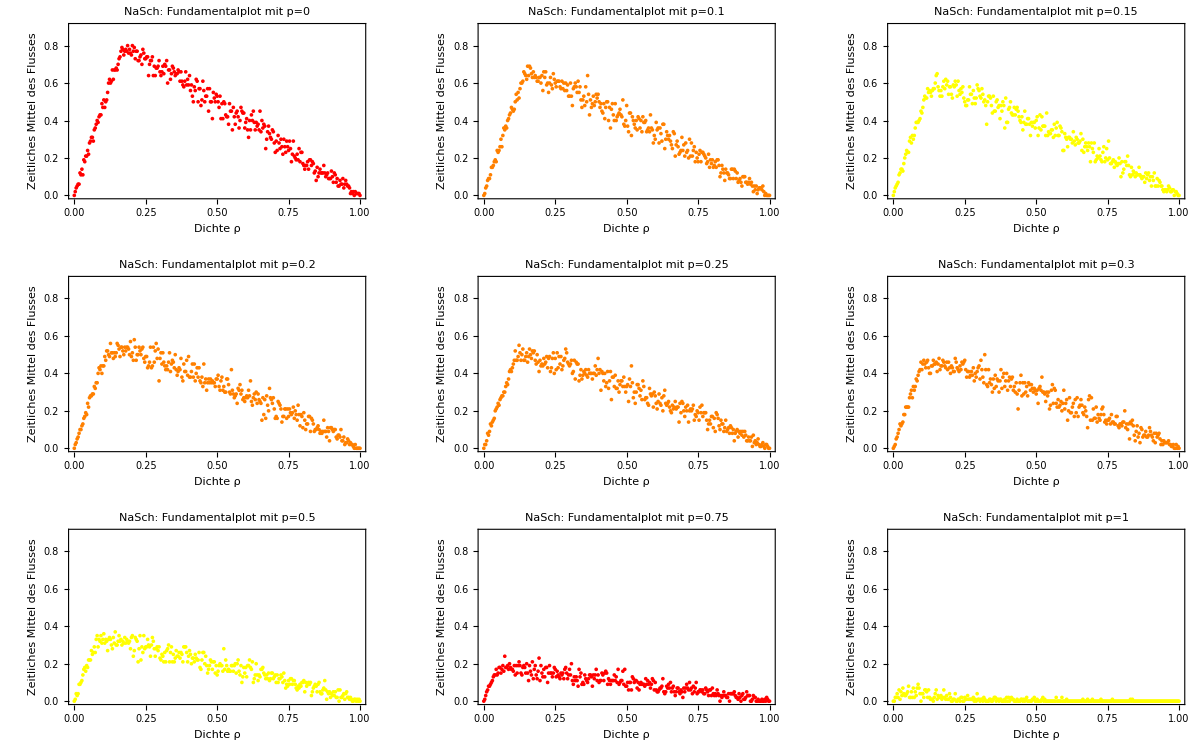

```mathematica
fundplot={};
AppendTo[fundplot,FundamentalD["NaSch",0,0]];
AppendTo[fundplot,FundamentalD["NaSch",0.1,0]];
AppendTo[fundplot,FundamentalD["NaSch",0.15,0]];
AppendTo[fundplot,FundamentalD["NaSch",0.2,0]];
AppendTo[fundplot,FundamentalD["NaSch",0.25,0]];
AppendTo[fundplot,FundamentalD["NaSch",0.3,0]];
AppendTo[fundplot,FundamentalD["NaSch",0.5,0]];
AppendTo[fundplot,FundamentalD["NaSch",0.75,0]];
AppendTo[fundplot,FundamentalD["NaSch",1,0]];

GraphicsGrid[Table[fundplot[[n]],{m,1,9,3},{n,m,m+2,1}],ImageSize->Full]
```

```mathematica
Clear[fundplot];
Clear[fundnasch60];
Clear[fundnasch100];
Clear[fundnasch200];
```

An den Fundamentalplots lässt sich erkennen, dass, je höher die Trödelwarscheinlichkeit ist, desto geringer ist der Höchstwert des Flusses.
Die Diagramme zeigen, dass die Höhe der Peaks für p=0.1 am höchsten ist und zwar fast bis 0.7. Für p=1 ist der höchste Wert des Flusses circa 0.012. 
Mit einem Unterschied von Δp=0.05 zwischen den Plots unterscheiden sich die jeweiligen Peaks um 0.5 und mit Δp=0.1 ist der Unterschied auch ungefähr 0.1.
Es lässt sich beobachten, dass der Fluss circa bis zur Dichte ρ=0.125 linear ansteigt, weil die Anzahl der Autos für die Entwicklung von Staus nicht groß genug ist. Über dieser Dichte entwickeln sich mehrere Staus und der Fluss fällt linear ab. Der Fluss ist 0 ungefähr etwas vor der Dichte ρ=1.
Eine Ausnahme bildet p=1, wofür der Fluss fast sofort abfällt ab einer Dichte nahe 0.

## VDR

In diesem Modul wird das NaSch-Modell in mit der Velocity Dependent Randomization umgeschrieben. Dies bewirkt, dass die Trödelwahrscheinlichkeit abhängig von der Geschwindigkeit ist. Sie ist für stehende Autos um q höher als sonst für fahrende. Dies soll ein Trödeln beim Anfahren simulieren.

```mathematica
(*Fundamentalplots des Velocity-Dependent-Randomization Modells*)
vdrNaSch[nCar_,nCells_,tMax_,vMax_,p_,q_]:=Module[
(*q ist zusätzliche Wahrscheinlichkeit zum Trödeln beim Anfahren*)

(*lokale Variablen*)
{xAutos,vAutos,dAutos,xvdr,vvdr,dvdr,minAuto,maxAuto},

(*Erzeugen Listen für x, v und d für jeden Zeitschritt*)
xvdr={};
vvdr={};
dvdr={};

(*Autos haben Position x und Geschwindigkeit v zum vorderen Auto*)
xAutos=Sort[RandomSample[Range[nCells],nCar]];
vAutos=RandomInteger[{1,vMax},nCar];

(*Abspeichern Anfangsaufstellung*)
AppendTo[xvdr,xAutos];
AppendTo[vvdr,vAutos];

(*Verkehrsregeln aus NaSch-Modell implementieren*)
For[i=1,i<tMax,i++, (*Anfangszustand ist i=0, insgesamt tMax Schritte*)

(*Oft verwendete Variablen*)
minAuto=Min[xAutos];
maxAuto=Max[xAutos];


(*Freie Zellen d vor dem Auto bis zum vorderen*)
dAutos=Table[If[xAutos[[n]]<maxAuto,xAutos[[n+1]]-xAutos[[n]]-1,nCells-xAutos[[n]]+minAuto-1],{n,nCar-1}];
AppendTo[dAutos,If[xAutos[[nCar]]<maxAuto,xAutos[[1]]-xAutos[[nCar]]-1,nCells-xAutos[[nCar]]+minAuto-1]];

(*R1: Beschleunigen, falls vMax noch nicht erreicht*)
vAutos=Table[Min[vAutos[[n]]+1,vMax],{n,nCar}];

(*R2: Abbremsen, falls v größer als Abstand d*)
vAutos=Table[Min[dAutos[[n]],vAutos[[n]]],{n,nCar}]; 

(*R3: Trödeln mit Wahrscheinlichkeit p*)(*Randomization, q=p0-p, p+q wahrscheinlichkeit dass sie trödeln falls die vorher v=0 hatten, p=wahrsch. v>0*)
vAutos=Table[If[vAutos[[n]]==0,If[RandomReal[{0,1}]<=p+q,vAutos[[n]],vAutos[[n]]],If[RandomReal[{0,1}]<=p,vAutos[[n]]=vAutos[[n]]-1,vAutos[[n]]]],{n,nCar}];
(*Wenn Auto steht ist p um q erhöht*)

(*R4: Fahren um vAutos Zellen*)
xAutos=Table[If[xAutos[[n]]+vAutos[[n]]<=nCells,xAutos[[n]]=xAutos[[n]]+vAutos[[n]],xAutos[[n]]=xAutos[[n]]+vAutos[[n]]-nCells],{n,nCar}];

(*Abspeichern in ausgegebene Variablen*)
AppendTo[xvdr,xAutos];
AppendTo[vvdr,vAutos];
(*Letzter Durchlauf der Schleife speichert vorletzten Abstand ab, deshalb außerhalb Schleife letztes Element abspeichern*)
AppendTo[dvdr,dAutos];
];
(*Erneute Berechnung für Endposition*)
minAuto=Min[xAutos];
maxAuto=Max[xAutos];

(*Berechnen Abstände im letzten Zeitschritt*)
dAutos=Table[If[xAutos[[n]]<maxAuto,xAutos[[n+1]]-xAutos[[n]]-1,nCells-xAutos[[n]]+minAuto-1],{n,nCar-1}];
AppendTo[dAutos,If[xAutos[[nCar]]<maxAuto,xAutos[[1]]-xAutos[[nCar]]-1,nCells-xAutos[[nCar]]+minAuto-1]];

(*Abspeichern in dvdr*)
AppendTo[dvdr,dAutos];

Return[{xvdr,vvdr,dvdr}]
]
```

```mathematica
(*Plots zum Untersuchen des VDR-Modells*)
vdrplots={};
AppendTo[vdrplots,vdhisto["vdrNaSch",{60,100},{100},0.15,0.2]];
AppendTo[vdrplots,vdhisto["vdrNaSch",{60,100},{100},0.15,0.4]];
AppendTo[vdrplots,dichteplot["vdrNaSch",100,0.15,0.2,10]];
AppendTo[vdrplots,dichteplot["vdrNaSch",100,0.15,0.4,10]];
AppendTo[vdrplots,FundamentalD["vdrNaSch",0.15,0.2]];
AppendTo[vdrplots,FundamentalD["vdrNaSch",0.3,0.2]];
```

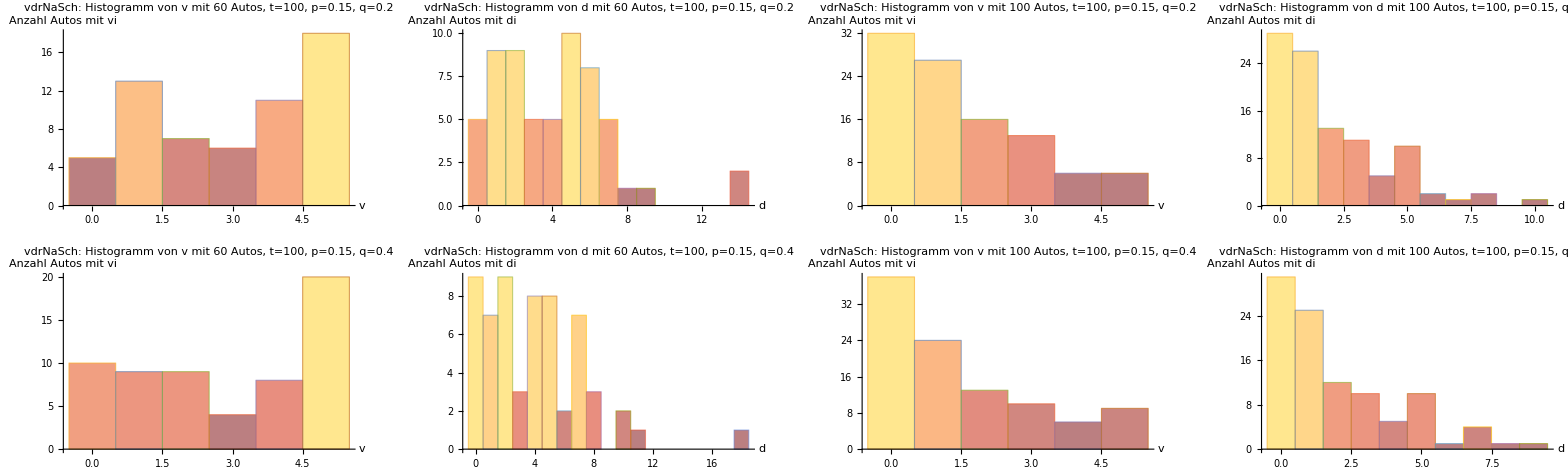

-Graphics-

```mathematica
vdrplots=Flatten[vdrplots];
GraphicsGrid[Table[vdrplots[[n]],{m,1,5,4},{n,m,m+3}],ImageSize->Full]
GraphicsGrid[Table[vdrplots[[n]],{m,9,11,2},{n,m,m+1}],ImageSize->Full]
```

```mathematica
Clear[vdrplots];
```

Aus den ersten zwei Histogrammen kann gefolgert werden, dass aufgrund von der geringeren Anzahl an Autos (60) über der Anzahl an Zellen (300) die Erhöhung der Trödelwahrscheinlichkeit q nicht häufig vorkommt, weil der Platz zwischen zwei Autos häufig höher ist als dessen Geschwindigkeit. 
Das passiert weniger bei einer höheren Anzahl an Fahrzeugen (z.B. 100 über 300), weil die Abstände geringer sind. Das verursacht eine Erhöhung der Trödelwahrscheinlichkeit um q, weshalb sich bilden Staus weiter ausbilden. Eine sehr geringe Menge an Autos haben einen größeren Abstand.
Bei 200 Autos ist letzteres nicht mehr erkennbar, die Abstände sind sehr gering.
Aus den nächsten Histogrammen, mit q erhöht zu 0.4, lässt sich beobachten, dass aufgrund der höheren Trödelwahrscheinlichkeit stehender Autos für 100 Autos mehr Autos eine geringere Geschwindigkeit haben im Vergleich zu q=0.2. Bei 60 Autos hingegen haben etwas über ein Drittel der Autos die Höchstgeschwindigkeit, da sich bei 60 Autos weniger Staus und damit Möglichkeiten dafür, dass Autos die Geschwindigkeit v=0 haben, bilden. 
Aus dem Dichteplot kann beobachtet werden, dass mit einer Wahrscheinlichkeit von q=0.2 die lokale Dichte der Autos mehrmals höher ist, es bilden sich größere Staus. Mit einer q=0.4 ist die lokale Dichte häufig höher auf der ganzen Straße, aber die Staus werden kürzer.
Die Fundamentalplots weisen keine großen Unterschiede zu denen des gewöhnlichen NaSch-Modells für p=0.15 und p=0.3 (s. oben) auf. Die zusätzliche Trödelwahrscheinlichkeit hat also auf den Fluss keinen bemerkbaren Einfluss.

## Zwei Spuren

Als letztes wird das NaSch-Modell auf zwei Spuren angepasst. Hierfür werden wie gewohnt zufällige Positionen für die angegebene Anzahl an Autos, nur hier auf zwei Spuren, generiert. Hierbei ist die Anzahl der Autos pro Spur auch zufällig. Nach der Abstandsberechnung und Schritt R1 aus dem NaSch-Modul, die Erhöhung der Geschwindigkeiten aller Autos, falls diese unter vMax liegen, wird für den neuen Schritt R2 ein zusätzliches Modul für den Spurwechsel aufgerufen. Das Wechseln der Spur entspricht hierbei dem Fahren einer Zelle, es wird danach also dem Auto die Geschwindigkeit v-1 oder 0 zugeteilt. Es wird von der rechten auf die linke Spur gewechselt, wenn folgende Bedingungen erfüllt sind: 
- die Geschwindigkeit des Autos ist größer als sein Abstand zum Vorderauto, 
- links befindet sich kein Auto auf der Nachbarzelle, 
- ein von hinten ankommendes Auto fährt mit einem möglichen Abbremsen um 1 höchstens auf die Zelle direkt hinter der Nachbarzelle links und
- das Auto selbst fährt mit einem möglichen Abbremsen um 1 höchstens auf die Zelle direkt hinter einem vorausfahrenden Auto auf der linken Spur. 
Nach diesem Schritt werden alle wechselnden Autos zunächst auf die Nachbarzelle auf der linken Spur positioniert, um zu vermeiden, dass während des Wechselvorganges ebenfalls wechselnde Autos überholt werden. 
Von der linken zur rechten Spur wird gewechselt, wenn diese Bedingungen erfüllt sind:
- die Nachbarzelle auf der rechten Spur ist frei,
- ein von hinten ankommendes Auto fährt mit einem möglichen Abbremsen um 1 höchstens auf die Zelle direkt hinter der Nachbarzelle rechts und 
- das Auto selbst fährt mit einem möglichen Abbremsen um 2 höchstens direkt hinter ein vorausfahrendes Auto auf der rechten Spur.
Danach erfolgt wieder der Spurwechsel von links nach rechts. Dass beim Wechsel nach rechts ein Abbremsen von 2 in Kauf genommen wird, statt wie beim Wechsel nach links nur um 1, soll das Rechtsfahrgebot annähernd in das Modell einbringen. Die zwei unterschiedlichen Werte haben nämlich den Effekt, dass mehr Autos nach rechts wechseln als nach links, da die Bedingungen auch für ein engeres Einordnen rechts offen sind. Aus dem Spurwechsel-Modul werden unter Anderem die neuen Listen der Positionen und Geschwindigkeiten ausgegeben, die in den nächsten drei aus dem NaSch-Modell übernommenen Regeln weiter verwendet werden.   
Zunächst werden die Abstände aktualisiert, dann in R3 die Geschwindigkeiten über den Abständen zu den Autos davor auf letztere herabgesetzt, in R4 mit der Trödelwahrscheinlichkeit p um 1 abgebremst und in R5 die Positionen der Autos aktualisiert.

```mathematica
(*Funktion für den Spurenwechsel*)
Spurwechsel[nCar_,nCells_,savexlist1_,savexlist2_,savevlist1_,savevlist2_,xlist1_,xlist2_,vlist1_,vlist2_,dlist1_,dlist2_,m1_,m2_]:=Module[
(*Lokale Variablen*)
{xAutos1,xAutos2,vAutos1,vAutos2,dAutos1,dAutos2,savexAutos1,savexAutos2,savevAutos1,savevAutos2,savekleinere,hinter,hinterx1,hinterx2,vorx1,
vorx2,hinterv1,hinterv2,vorv1,vorv2,auto,vauto,autoindex,index1,index2,nachindex1,hinterautos,wechselvon1,wechselzu1,wechselvon2,wechselzu2,
nachindex2,hinterstrecke1,hinterstrecke2,vorstrecke1,vorstrecke2,fahrt1,fahrt2,laengesx1,laengesx2,laengex1,laengex2,k,h,newm1,newm2},

(*In twolanesNaSch falls leere Liste mit {0.5} gefüllt, hierfür wieder leer benötigt*)
xAutos1=xlist1;xAutos2=xlist2;
vAutos1=vlist1;vAutos2=vlist2;
dAutos1=dlist1;dAutos2=dlist2;
savexAutos1=savexlist1;
savexAutos2=savexlist2;
savevAutos1=savevlist1;
savevAutos2=savevlist2;
laengesx1=Length[savexAutos1];
laengesx2=Length[savexAutos2];
newm1=m1;newm2=m2;
wechsel1=0;wechsel2=0;
wechselzu1={};wechselvon1={};
wechselzu2={};wechselvon2={};

(*Wechsel rechte Spur zu linker*)
  (*Falls Auto auf rechter Spur*)
  If[laengesx1>0,
  k=1;
  Do[
  ((*Betrachtetes Auto*)
  auto=savexAutos1[[k]];
  vauto=savevAutos1[[k]];
  laengex1=Length[xAutos1];
  laengex2=Length[xAutos2];
  (*savevAutos nach Beschleunigung, dAutos bleiben im Wechselvorgang zunächst unverändert*)
  (*Falls v kleiner/gleich d oder Nachbarzelle links besetzt wird nächstes Auto auf rechter Spur betrachtet*)
  Which[vauto<=dAutos1[[k]]||!Select[savexAutos2,#==auto &]=={},k=k+1;,
  (*Wenn hier sind beide zuvor nicht erfüllt*)
  laengesx2>0,
  (savekleinere=Select[savexAutos2,#<auto &];
  (*Falls links nur Auto weiter vorne oder am anderem Straßenende*)
  Which[savekleinere=={},
  ((*Auto von hinten ist am anderen Straßenende*)
  index2=Flatten[Position[savexAutos2,Max[savexAutos2]]][[1]];
  (*Abspeichern x und v des Autos von hinten*)
  hinterx2=savexAutos2[[index2]];
  hinterv2=savevAutos2[[index2]];
  (*Strecke des Autos am anderen Straßenende links mit Abbremsen um 1*)
  hinterstrecke2=hinterx2+hinterv2-1-nCells;
  (*Entweder überquert letzte Zelle nicht -> immer hinterstrecke<fahrt1; oder überquert letzte Zelle -> möglich hinterstrecke<fahrt1*)),
  (*Es gibt Auto mit kleinerer Position*)
  !savekleinere=={},
  ((*Index von hinten ankommendes Auto*)
  index2=Flatten[Position[savexAutos2,Max[savekleinere]]][[1]];
  (*Abspeichern x und v des Autos von hinten*)
  hinterx2=savexAutos2[[index2]];
  hinterv2=savevAutos2[[index2]];
  hinterstrecke2=Which[hinterx2+hinterv2-1<=nCells,hinterx2+hinterv2-1,hinterx2+hinterv2-1>nCells,hinterx2+hinterv2-1-nCells];)
  ];
  (*Index vorherfahrendes Auto*)
  nachindex2=Which[index2<laengesx2,index2+1,index2==laengesx2,1];
  (*Abspeichern x und v des vorfahrenden Autos*)
  vorx2=savexAutos2[[nachindex2]];
  vorv2=savevAutos2[[nachindex2]];
  (*Strecke des vorfahrenden Autos links*)
  vorstrecke2=Which[vorx2+vorv2<=nCells,vorx2+vorv2,vorx2+vorv2>nCells,vorx2+vorv2-nCells];
  (*Weiterfahrt nach Wechsel (v-1) nach links mit möglichem zusätzlichen Abbremsen um 1 -> -2*)
  fahrt1=Which[vauto<=2,auto,auto+vauto-2<=nCells,auto+vauto-2,auto+vauto-2>nCells,auto+vauto-2-nCells];
  If[hinterstrecke2<fahrt1 && fahrt1<vorstrecke2,
  (*Index des von hinten kommenden Autos, falls vorhanden*)
  (*Falls links leer, an erster Stelle einfügen*)
  hinter=Which[laengex2==0,0,
  (*Falls Auto mit kleinerer Position, an Position danach*)
  !Select[xAutos2,#<auto &]=={},
  Flatten[Position[xAutos2,Max[Select[xAutos2,#<auto &]]]][[1]],
  Select[xAutos2,#<auto &]=={},
  (*Falls kein Auto kleiner, an Stelle vor kleinstes Auto*)
  Flatten[Position[xAutos2,Min[xAutos2]]][[1]]-1];
  xAutos2=Insert[xAutos2,auto,hinter+1];
  vAutos2=Insert[vAutos2,vauto,hinter+1];
  (*Index für Flussberechnung mit FundamentalD*)
  newm2=Which[newm2==0||hinter+1<=newm2,newm2+1,hinter+1>newm2,newm2];
  AppendTo[wechselzu2,auto];
  (*Element aus xAutos1 entfernen*)
  autoindex=Flatten[Position[xAutos1,auto]][[1]];
  xAutos1=Delete[xAutos1,autoindex];
  vAutos1=Delete[vAutos1,autoindex];
  newm1=Which[autoindex>newm1,newm1,newm1>1,newm1-1,newm1<=1,Length[xAutos1]];
  AppendTo[wechselvon1,auto];
  ];
  k=k+1;),
  (*Links leer,Wechsel*)
  laengesx2==0,
  ((*Index zum Einfügen in xAutos2*)
  (*Gleich zu oben*)
  hinter=Which[laengex2==0,0,
  !Select[xAutos2,#<auto &]=={},
  Flatten[Position[xAutos2,Max[Select[xAutos2,#<auto &]]]][[1]],
  Select[xAutos2,#<auto &]=={},
  Flatten[Position[xAutos2,Min[xAutos2]]][[1]]-1];
  xAutos2=Insert[xAutos2,auto,hinter+1];
  vAutos2=Insert[vAutos2,vauto,hinter+1];
  (*Index für Flussberechnung mit FundamentalD*)
  Which[newm2==0||hinter+1<=newm2,(newm2=newm2+1;wechsel2=wechsel2+1;),hinter+1>newm2,newm2=newm2];
  AppendTo[wechselzu2,auto];
  (*Element aus xAutos1 entfernen*)
  autoindex=Flatten[Position[xAutos1,auto]][[1]];
  xAutos1=Delete[xAutos1,autoindex];
  vAutos1=Delete[vAutos1,autoindex];
  newm1=Which[autoindex>newm1,newm1,newm1>1,newm1-1,newm1<=1,Length[xAutos1]];
  AppendTo[wechselvon1,auto];
  k=k+1;)];
  (*Nicht mehr gebrauchte Variablen clearen*)
  Clear[auto,vauto,savekleinere,index2,nachindex2,hinterx2,hinterv2,vorx2,vorv2,hinterstrecke2,vorstrecke2,fahrt1,hinter,autoindex];)
  ,laengesx1];
  ];
  
  (*Wechsel linke Spur zu rechter*)
  (*Falls Auto auf linker Spur*)
  If[laengesx2>0,
  h=1;
  Do[
  ((*Betrachtetes Auto*)
  auto=savexAutos2[[h]];
  vauto=savevAutos2[[h]];
  laengex1=Length[xAutos1];
  laengex2=Length[xAutos2];
  (*Falls Nachbarzelle rechts besetzt wird nächstes Auto auf linker Spur betrachtet*)
  Which[!Select[savexAutos1,#==auto &]=={},h=h+1;,
  laengesx1>0,
  (savekleinere=Select[savexAutos1,#<auto &];
  (*Falls rechts nur Auto weiter vorne oder am anderem Straßenende*)
  Which[savekleinere=={},
  ((*Auto von hinten ist am anderen Straßenende*)
  index1=Flatten[Position[savexAutos1,Max[savexAutos1]]][[1]];
  (*Abspeichern x und v des Autos von hinten*)
  hinterx1=savexAutos1[[index1]];
  hinterv1=savevAutos1[[index1]];
  (*Strecke des Autos am anderen Straßenende rechts mit Abbremsen um 1*)
  hinterstrecke1=hinterx1+hinterv1-1-nCells;
  (*Entweder überquert letzte Zelle nicht -> immer hinterstrecke<fahrt1; oder überquert letzte Zelle -> möglich hinterstrecke<fahrt1*)),
  (*Es gibt Auto mit kleinerer Position*)
  !savekleinere=={},
  ((*Index von hinten ankommendes Auto*)
  index1=Flatten[Position[savexAutos1,Max[savekleinere]]][[1]];
  (*Abspeichern x und v des Autos von hinten*)
  hinterx1=savexAutos1[[index1]];
  hinterv1=savevAutos1[[index1]]; 
  hinterstrecke1=Which[hinterx1+hinterv1-1<=nCells,hinterx1+hinterv1-1,hinterx1+hinterv1-1>nCells,hinterx1+hinterv1-1-nCells];)
  ];
  (*Index vorherfahrendes Auto*)
  nachindex1=Which[index1<laengesx1,index1+1,index1==laengesx1,1];
  (*Abspeichern x und v des vorfahrenden Autos*)
  vorx1=savexAutos1[[nachindex1]];
  vorv1=savevAutos1[[nachindex1]];
  (*Strecke des vorfahrenden Autos rechts*)
  vorstrecke1=Which[vorx1+vorv1<=nCells,vorx1+vorv1,vorx1+vorv1>nCells,vorx1+vorv1-nCells];
  (*Weiterfahrt nach Wechsel (v-1) nach rechts mit möglichem zusätzlichen Abbremsen um 2 -> -3*)
  fahrt2=Which[vauto<=3,auto,auto+vauto-3<=nCells,auto+vauto-3,auto+vauto-3>nCells,auto+vauto-3-nCells];
  If[hinterstrecke1<fahrt2 && fahrt2<vorstrecke1,
  (*Index des von hinten kommenden Autos, falls vorhanden*)
  hinterautos=Select[xAutos1,#<auto &];
  (*Falls rechts leer, an erster Stelle einfügen*)
  hinter=Which[laengex1==0,0,
  (*Falls Auto mit kleinerer Position, an Position danach*)
  !hinterautos=={},
  Flatten[Position[xAutos1,Max[hinterautos]]][[1]],
  hinterautos=={},
  (*Falls kein Auto kleiner, an Stelle vor kleinstes Auto*)
  Flatten[Position[xAutos1,Min[xAutos1]]][[1]]-1]; 
  xAutos1=Insert[xAutos1,auto,hinter+1];
  vAutos1=Insert[vAutos1,vauto,hinter+1];
  (*Index für Flussberechnung mit FundamentalD*)
  newm1=Which[newm1==0||hinter+1<=newm1,newm1+1,hinter+1>newm1,newm1];
  AppendTo[wechselzu1,auto];
  (*Element aus xAutos2 entfernen*)
  autoindex=Flatten[Position[xAutos2,auto]][[1]];
  xAutos2=Delete[xAutos2,autoindex];
  vAutos2=Delete[vAutos2,autoindex];
  newm2=Which[autoindex>newm2,newm2,newm2>1,newm2-1,newm2<=1,Length[xAutos2]];
  AppendTo[wechselvon2,auto];
  ];
  h=h+1;),
  (*Rechts leer,Wechsel*)
  laengesx1==0,
  ((*Index zum Einfügen in xAutos1*)
  hinterautos=Select[xAutos1,#<auto &];
  (*Gleich zu oben*)
  hinter=Which[laengex1==0,0,
  !hinterautos=={},
  Flatten[Position[xAutos1,Max[hinterautos]]][[1]],
  hinterautos=={},
  Flatten[Position[xAutos1,Min[xAutos1]]][[1]]-1];
  xAutos1=Insert[xAutos1,auto,hinter+1];
  vAutos1=Insert[vAutos1,vauto,hinter+1];
  (*Index für Flussberechnung mit FundamentalD*)
  newm1=Which[newm1==0||hinter+1<=newm1,newm1+1,hinter+1>newm1,newm1];
  AppendTo[wechselzu1,auto];
  (*Element aus xAutos2 entfernen*)
  autoindex=Flatten[Position[xAutos2,auto]][[1]];
  xAutos2=Delete[xAutos2,autoindex];
  vAutos2=Delete[vAutos2,autoindex];
  newm2=Which[autoindex>newm2,newm2,newm2>1,newm2-1,newm2<=1,Length[xAutos2]];
  AppendTo[wechselvon2,auto];
  h=h+1;)];
  (*Nicht mehr gebrauchte Variablen clearen*)
  Clear[auto,vauto,savekleinere,index1,nachindex1,hinterx1,hinterv1,vorx1,vorv1,hinterstrecke1,vorstrecke1,fahrt2,hinter,autoindex];)
  ,laengesx2];
  ];

Return[{xAutos1,xAutos2,vAutos1,vAutos2,newm1,newm2,wechselvon1,wechselzu1,wechselvon2,wechselzu2}]
]
```

```mathematica
(*Modell zwei Fahrspuren*)
twolanesNaSch[nCar_,nCells_,tMax_,vMax_,p_]:=Module[

(*lokale Variablen*)
{xAutos,xAutos1,xAutos2,vAutos1,vAutos2,dAutos1,dAutos2,xtwolan1,xtwolan2,vtwolan1,vtwolan2,dtwolan1,dtwolan2,
savex1,savex2,savev1,savev2,saved1,saved2,save,maxAuto1,minAuto1,maxAuto2,minAuto2,m1,m2,wechselvon1,wechselzu1,
wechselvon2,wechselzu2,laengesx1,laengesx2,laengex1,laengex2,a,k,h,mlist1,mlist2,data},

(*Listen zur Ausgabe der Daten*)
xtwolan1={};
xtwolan2={};
vtwolan1={};
vtwolan2={};
dtwolan1={};
dtwolan2={};

(*NaSch-Modell*)

(*Autos haben Position x und Geschwindigkeit v zum vorderen Auto*)
(*Erstellen Liste xAutos mit doppelter Länge als Straße*)
xAutos=Sort[RandomSample[Range[2 nCells],nCar]];
(*Aufteilen Liste in zwei Spuren, 1 rechts, 2 links*)
xAutos1=Select[xAutos,#<=nCells &];
(*Positionen der linken Spur setzen in Bereich von 0 bis nCells*)
xAutos2=Which[xAutos1!={},Drop[Table[xAutos[[n]]-nCells,{n,nCar}],Length[xAutos1]],xAutos1=={},Table[xAutos[[n]]-nCells,{n,nCar}]];
(*Geschwindigkeiten für alle Autos getrennt auf den Spuren*);
vAutos1=RandomInteger[{1,vMax},Length[xAutos1]];
vAutos2=RandomInteger[{1,vMax},Length[xAutos2]];

(*Abspeichern Ausgangssituation*)
AppendTo[xtwolan1,Which[xAutos1!={},xAutos1,xAutos1=={},{0.5}]];
AppendTo[xtwolan2,Which[xAutos2!={},xAutos2,xAutos2=={},{0.5}]];
AppendTo[vtwolan1,Which[vAutos1!={},vAutos1,vAutos1=={},{0.5}]];
AppendTo[vtwolan2,Which[vAutos2!={},vAutos2,vAutos2=={},{0.5}]];
savex1=xAutos1;
savex2=xAutos2;

(*Index zur Betrachtung des Flusses*)
m1=Length[xAutos1];
m2=Length[xAutos2];
mlist1={};
mlist2={};
AppendTo[mlist1,m1];
AppendTo[mlist2,m2];

(*Liste Positionen der Wechsel*)
wechselvon1={};
wechselzu1={};
wechselvon2={};
wechselzu2={};

(*Verkehrsregeln aus NaSch-Modell implementieren*)
For[t=2,t<=tMax,t++, (*Ausgangssituation ist t=1*)

(*Oft verwendete Variablen*)
(*Listen des Zeitschritts davor*)
laengex1=Length[xAutos1];
laengex2=Length[xAutos2];
laengesx1=Length[savex1];
laengesx2=Length[savex2];
maxAuto1=Max[xAutos1];
minAuto1=Min[xAutos1];
maxAuto2=Max[xAutos2];
minAuto2=Min[xAutos2];


  (*Freie Zellen d vor dem Auto bis zum vorderen*)
  (*Rechte Spur*)
  Which[laengex1>1,
  (dAutos1=Table[If[xAutos1[[n]]<maxAuto1,xAutos1[[n+1]]-xAutos1[[n]]-1,nCells-xAutos1[[n]]+minAuto1-1],{n,laengex1-1}];
  AppendTo[dAutos1,If[xAutos1[[laengex1]]<maxAuto1,xAutos1[[1]]-xAutos1[[laengex1]]-1,nCells-xAutos1[[laengex1]]+xAutos1[[1]]-1]];),
  laengex1==1,
  dAutos1={nCells-1};,
  laengex1==0,
  dAutos1={};
  AppendTo[dAutos1,{0.5}];]; (*Eigentlich hinzufügen zu dtwolan1*)
   
  (*Linke Spur*)
  Which[laengex2>1,
  (dAutos2=Table[If[xAutos2[[n]]<maxAuto2,xAutos2[[n+1]]-xAutos2[[n]]-1,nCells-xAutos2[[n]]+minAuto2-1],{n,laengex2-1}]; 
  AppendTo[dAutos2,If[xAutos2[[laengex2]]<maxAuto2,xAutos2[[1]]-xAutos2[[laengex2]]-1,nCells-xAutos2[[laengex2]]+xAutos2[[1]]-1]];),
  laengex2==1,
  dAutos2={nCells-1};,
  laengex2==0,
  dAutos2={};
  AppendTo[dAutos2,{0.5}];]; (*Eigentlich hinzufügen zu dtwolan2*)
  
  (*Abspeichern Abstände*)
  AppendTo[dtwolan1,dAutos1];
  AppendTo[dtwolan2,dAutos2];
  
  (*R1: Beschleunigen, falls vMax noch nicht erreicht*)
  (*Rechte Spur*)
  If[laengex1>0,
  vAutos1=Table[Min[vAutos1[[n]]+1,vMax],{n,laengex1}];,
  vAutos1={};
  AppendTo[vtwolan1,{0.5}];
  ];
  savev1=vAutos1;

  (*Linke Spur*)
  If[laengex2>0,
  vAutos2=Table[Min[vAutos2[[n]]+1,vMax],{n,laengex2}];,
  vAutos2={};
  AppendTo[vtwolan2,{0.5}];
  ];
  savev2=vAutos2;

  data=Spurwechsel[nCar,nCells,savex1,savex2,savev1,savev2,xAutos1,xAutos2,vAutos1,vAutos2,dAutos1,dAutos2,m1,m2];
  xAutos1=data[[1]];xAutos2=data[[2]];
  vAutos1=data[[3]];vAutos2=data[[4]];
  m1=data[[5]];m2=data[[6]];
  AppendTo[mlist1,m1];AppendTo[mlist2,m2];
  Which[data[[7]]!={},AppendTo[wechselvon1,data[[7]]],data[[7]]=={},AppendTo[wechselvon1,{nCells+1}]];
  Which[data[[8]]!={},AppendTo[wechselzu1,data[[8]]],data[[8]]=={},AppendTo[wechselzu1,{nCells+1}]];
  Which[data[[9]]!={},AppendTo[wechselvon2,data[[9]]],data[[9]]=={},AppendTo[wechselvon2,{nCells+1}]];
  Which[data[[10]]!={},AppendTo[wechselzu2,data[[10]]],data[[10]]=={},AppendTo[wechselzu2,{nCells+1}]];
  Clear[data];
  
  (*Berechnungen für neue xAutos*)
  laengex1=Length[xAutos1];
  laengex2=Length[xAutos2];
  maxAuto1=Max[xAutos1];
  minAuto1=Min[xAutos1];
  maxAuto2=Max[xAutos2];
  minAuto2=Min[xAutos2];
  
  (*Nach Spurwechsel freie Zellen d vor dem Auto bis zum vorderen*)
  (*Rechte Spur*)
  Clear[dAutos1];
  Which[laengex1>1,
  (dAutos1=Table[If[xAutos1[[n]]<maxAuto1,xAutos1[[n+1]]-xAutos1[[n]]-1,nCells-xAutos1[[n]]+minAuto1-1],{n,laengex1-1}];
  AppendTo[dAutos1,If[xAutos1[[laengex1]]<maxAuto1,xAutos1[[1]]-xAutos1[[laengex1]]-1,nCells-xAutos1[[laengex1]]+xAutos1[[1]]-1]];),
  laengex1==1,
  dAutos1={nCells-1};,
  laengex1==0,
  dAutos1={0.5};];
   
  (*Linke Spur*)
  Clear[dAutos2];
  Which[laengex2>1,
  (dAutos2=Table[If[xAutos2[[n]]<maxAuto2,xAutos2[[n+1]]-xAutos2[[n]]-1,nCells-xAutos2[[n]]+minAuto2-1],{n,laengex2-1}]; 
  AppendTo[dAutos2,If[xAutos2[[laengex2]]<maxAuto2,xAutos2[[1]]-xAutos2[[laengex2]]-1,nCells-xAutos2[[laengex2]]+xAutos2[[1]]-1]];),
  laengex2==1,
  dAutos2={nCells-1};,
  laengex2==0,
  dAutos2={0.5};
  ];
   
  (*R3: Abbremsen, falls v größer als Abstand d*)
  (*Rechte Spur*)
  If[laengex1>0,
  vAutos1=Table[Min[dAutos1[[n]],vAutos1[[n]]],{n,laengex1}];
  ];
  (*Linke Spur*)
  If[laengex2>0,
  vAutos2=Table[Min[dAutos2[[n]],vAutos2[[n]]],{n,laengex2}];
  ];
  
  (*R4: Trödeln mit Wahrscheinlichkeit p*)
  (*Rechte Spur*)
  If[laengex1>0,
  vAutos1=Table[If[RandomReal[{0,1}]<=p,vAutos1[[n]]=Max[vAutos1[[n]]-1,0],vAutos1[[n]]],{n,laengex1}]; 
  ];
  (*Linke Spur*)
  If[laengex2>0,
  vAutos2=Table[If[RandomReal[{0,1}]<=p,vAutos2[[n]]=Max[vAutos2[[n]]-1,0],vAutos2[[n]]],{n,laengex2}];
  ];
  
  (*R5: Fahren um vAutos Zellen*)
  (*Rechte Spur*)
  If[laengex1>0,
  xAutos1=Table[If[xAutos1[[n]]+vAutos1[[n]]<=nCells,xAutos1[[n]]=xAutos1[[n]]+vAutos1[[n]],xAutos1[[n]]=xAutos1[[n]]+vAutos1[[n]]-nCells],{n,laengex1}];
  ];
 
  (*Linke Spur*)
  If[laengex2>0,
  xAutos2=Table[If[xAutos2[[n]]+vAutos2[[n]]<=nCells,xAutos2[[n]]=xAutos2[[n]]+vAutos2[[n]],xAutos2[[n]]=xAutos2[[n]]+vAutos2[[n]]-nCells],{n,laengex2}];
  ];
  (*Abspeichern xAutos für nächsten Zeitschritt*)
  savex1=xAutos1;
  savex2=xAutos2;
  
  (*Abspeichern Daten in Listen zur Ausgabe*)
  AppendTo[xtwolan1,Which[xAutos1!={},xAutos1,xAutos1=={},{0.5}]];
  AppendTo[xtwolan2,Which[xAutos2!={},xAutos2,xAutos2=={},{0.5}]];
  AppendTo[vtwolan1,Which[vAutos1!={},vAutos1,vAutos1=={},{0.5}]];
  AppendTo[vtwolan2,Which[vAutos2!={},vAutos2,vAutos2=={},{0.5}]];
  
  ];
  
  (*Abspeichern Abstände nach Spurwechsel in letztem Schritt*)
  AppendTo[dtwolan1,dAutos1];
  AppendTo[dtwolan2,dAutos2];
 
Return[{xtwolan1,xtwolan2,vtwolan1,vtwolan2,dtwolan1,dtwolan2,wechselvon1,wechselzu1,wechselvon2,wechselzu2}]
]
```

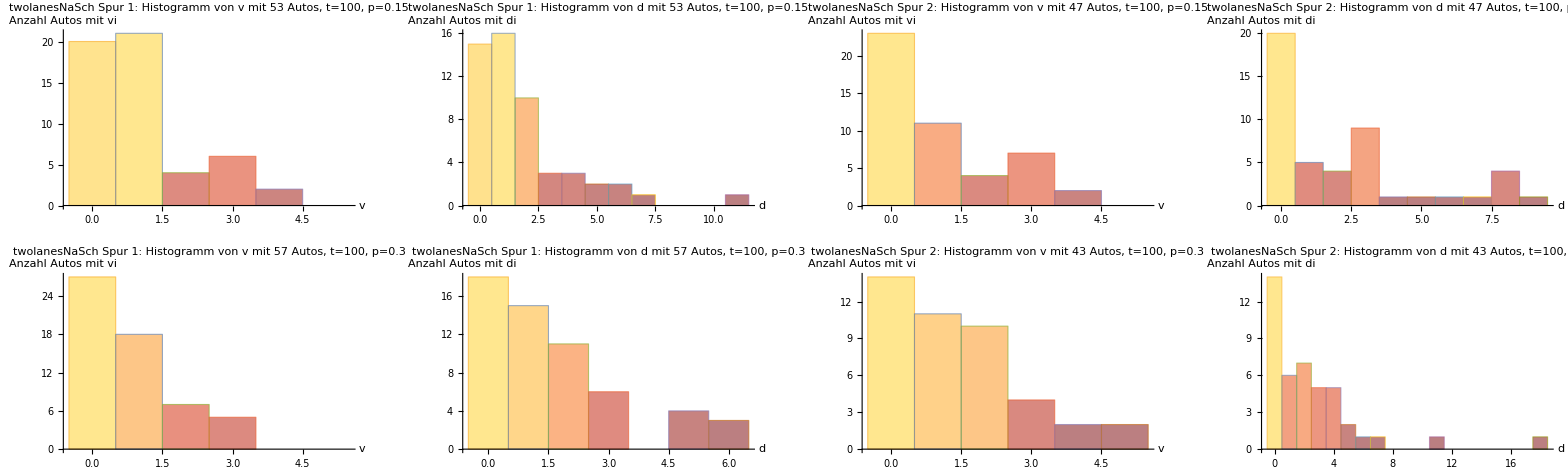

-Graphics-

```mathematica
(*Erwartete Laufzeit pro Fundamentalplot sind 6-7 Minuten*)
twolanesplots={};
(*Histogramme und Dichteplots für die Spuren getrennt*)
AppendTo[twolanesplots,vdhisto2D[{100},{100},0.15]];
AppendTo[twolanesplots,vdhisto2D[{100},{100},0.3]];
AppendTo[twolanesplots,dichteplot2D[100,0.15,10]];
AppendTo[twolanesplots,dichteplot2D[100,0.3,10]];
AppendTo[twolanesplots,FundamentalD["twolanesNaSch",0.15,0]];
AppendTo[twolanesplots,FundamentalD["twolanesNaSch",0.3,0]];

GraphicsGrid[Table[Flatten[twolanesplots][[n]],{m,1,5,4},{n,m,m+3}],ImageSize->Full]
GraphicsGrid[Table[Flatten[twolanesplots][[n]],{m,9,13,2},{n,m,m+1}],ImageSize->Full]
```

Beim Vergleich der Histogramme der zwei Spuren fällt auf, dass sowohl für p=0.15 als auch für p=0.3 auf der linken Spur einen größerer Anteil der Autos Geschwindigkeiten über 0 und Abstände größer als 0 hat als auf der rechten Spur. Dies kann auf die Bedingungen zum Spurwechsel zurückgeführt werden, die beim Wechsel nach links ein eigenes Abbremsen von 1 und beim Wechsel nach rechts eins um 2 in Kauf nehmen. Somit pendelt sich mit der Zeit eine höhere mittlere Geschwindigkeit auf der linken Spur ein.
Bei den Dichteplots für p=0.15 lässt sich sowohl für die rechte als auch die linke Spur ein größerer Stau anfangs im 6.-8. Intervall erkennen, nach dem sich Rückstaus bilden. Auf der rechten Spur liegt der Höchstwert pro Intervall bei 9 Autos, links nur bei 8 Autos. Außerdem sind im Plot der linken Spur mehr dunkelrote Punkte zu sehen, also weniger besetzte Intervalle mit 0-1 Autos, als auf der rechten Spur, dessen Großteil orange (3-4 Autos) gefärbt ist. Für p=0.3 sind die gelben Ansammlungen von Autos mit 8 Autos auf der rechten Spur und 7 auf der linken breiter verteilt. Auf der rechten Spur ist der Großteil der Intervalle mit 4-8 Autos besetzt, wobei Intervalle mit 0-1 Autos sehr selten vertreten sind. Auf der linken Spur allerdings sind im Großteil der Intervalle 3-6 Autos enthalten, wobei auch Intervalle mit 0-1 Autos häufiger vertreten sind.
Bei den Fundamentalplots fällt auf, dass diese nicht mehr die charakteristische Form des linearen Anstiegs bis zur kritischen Dichte mit einem linearen Abfall danach haben. Für zwei Spuren steigt der Fluss wie bei einer Spur bis zu einer kritischen Dichte, hier bei circa ρ=0.1, mit hoher Steigung linear an. Hiernach steigt der Fluss mit etwas niedrigerer Steigung weiter bis zur Dichte circa bei ρ=0.45, wonach der Fluss bis ρ=0.9 mit kleiner Steigung abfällt. Der mittlere Teil mit kleinem Zuwachs/Abfall ähnelt einer gestauchten, nach unten geöffneten Parabel und der Höchstwert des Flusses liegt für beide bei circa 1. Nach ρ=0.9 fällt der Fluss wieder stark ab, da bei fast vollständiger Besetzung fließender Verkehr zunehmend unwahrscheinlich wird. Der höhere Fluss auch nach der kritischen Dichte für eine Spur bei ρ=0.125 lässt sich dadurch erklären, dass ausgebremste Autos auf die linke Spur ausweichen können, auf der sich länger und für höhere Dichten fließender Verkehr ausbilden kann, da durch die Wechselbedingungen ein Wechsel nach rechts priorisiert wird und sich somit eher dort Autos ansammeln.